#### Not Applicable If : The incident points alternate on the curve and plane mirror, there is no consecutive incidents of light on the either curve or x axis Applicable Cases: No knowledge of source point of light, there can be multiple incidents on the same point, light can retrace its path back

Incident points input and their plot

{{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}}

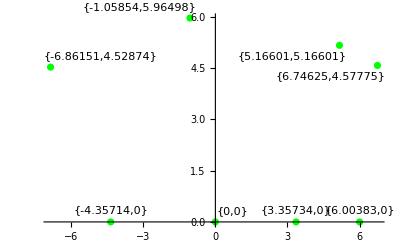

```mathematica
intersecpts = {{5.166010488516726,5.166010488516724},{6.003831069285709,0},{6.746248565974317,4.577754071440296},{3.357339206799729,0},{-1.058536173181429,5.964984411564576},{-4.357140119563605,0},{-6.861508969064321,4.528740458357809}, {0,0}}
intersecplot = ListPlot[Labeled[#,#] &/@ intersecpts, PlotRange->Full,PlotStyle->{Green}]
```

Separate the points into x -axis (plane mirror points) and unknown reflecting curve incident points

curvepts = {{-6.86151,4.52874},{-1.05854,5.96498},{5.16601,5.16601},{6.74625,4.57775}}

xaxispts = {{-4.35714,0},{0,0},{3.35734,0},{6.00383,0}}

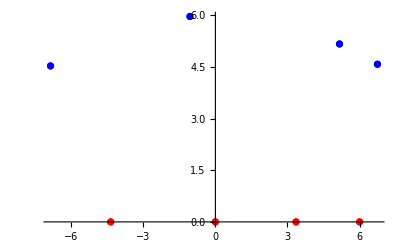

```mathematica
For[xaxispts = {}; i=0, i<Length[intersecpts], i++; If[intersecpts[[i, 2]]==0, AppendTo[xaxispts, intersecpts[[i]]]]]
curvepts = Sort[DeleteCases[intersecpts, Alternatives @@ xaxispts]];
xaxispts = Sort[xaxispts];
Print["curvepts = ", curvepts]
Print["xaxispts = ", xaxispts]
intersecplot2 = ListPlot[{#} & /@ intersecpts, PlotRange->Full,PlotStyle->{Blue, Red, Blue, Red, Blue, Red, Blue, Red}]
```

Function for initial 3 point tuple permutations

```mathematica
pttuplefunc[domainls_, codomainls_]:=
	Module[{tupleset={}},
	For[i=0, i<Length[domainls], i++;
		For[j=0, j<Length[codomainls], j++;
			For[k=0, k<Length[domainls], k++;
				tupleset = AppendTo[tupleset, {domainls[[i]],codomainls[[j]], domainls[[k]]}];
			]]];
	Return[tupleset, Module]];
```

Path permutations till the first plane mirror reflection

```mathematica
tuple3point = pttuplefunc[xaxispts, curvepts]
Print["No of tuples = ", Length[tuple3point]]
```

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

No of tuples = 64

Next we check check reflections and eliminate paths based on it

```mathematica
(*Function to check for the curve points lying on the reflected ray *)
reflecdrop[domainls_] := 
	Module[{tupleset = {}}, 
		For[i=0, i<Length[domainls], i++;
			For[(eqn = y == -(Last[List @@ Reduce[y - InterpolatingPolynomial[{Part[domainls[[i]],-2], Part[domainls[[i]],-1]},x]==0,y]]));
				j=0, j<Length[curvepts], j++;
				If[(eqn /. {x->curvepts[[j,1]], y->curvepts[[j,2]]})== True, 
					tupleset = AppendTo[tupleset,Join[domainls[[i]], {curvepts[[j]]}]]]]];
	Return[tupleset, Module]];
```

Out of 64 paths, after elimination we have 24 paths after the 1st reflection on plane mirror

```mathematica
a = reflecdrop[tuple3point];
a
```

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}}}

```mathematica
path2func[path_]:= 
	Module[{tupleset={}},
		For[tupleset={};i=0, i<Length[path], i++;
			For[j=0, j<Length[xaxispts], j++;
				tupleset = Append[tupleset, Join[path[[i]], {xaxispts[[j]]}]]]; Print[tupleset]];
		Return[tupleset, Module]];
```

```mathematica
merge[list_]:=Module[{a= reflecdrop[list]}, Return[path2func[a], Module]];
function[list_]:= Module[{a, new={}},
	If[EvenQ[Length[intersecpts]]==True, a = reflecdrop[Nest[merge, list, (Length[intersecpts]-4)/2]],a = Nest[merge, list, (Length[intersecpts]-3)/2]];
	For[i=0, i<Length[a], i++;
	If[CountDistinct[a[[i]]]==Length[intersecpts], new = AppendTo[new, a[[i]]]]];
	Return[new, Module]];
```

```mathematica
finalpath = function[tuple3point]
```

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}}}

{{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{-4.35714,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{-4.35714,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{0,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{3.35734,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{6.00383,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{-4.35714,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{0,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{3.35734,0}},{{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{-4.35714,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{0,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}},{{6.00383,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{6.00383,0}}}

{{{0,0},{-6.86151,4.52874},{-4.35714,0},{-1.05854,5.96498},{3.35734,0},{6.74625,4.57775},{6.00383,0},{5.16601,5.16601}},{{0,0},{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{-1.05854,5.96498},{-4.35714,0},{-6.86151,4.52874}}}

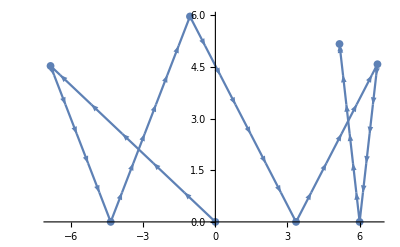

```mathematica
ListLinePlot[finalpath[[1]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
```

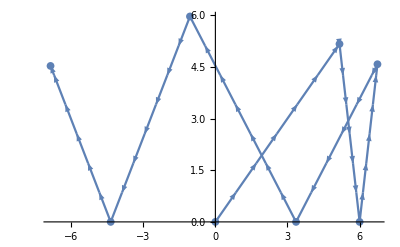

```mathematica
ListLinePlot[finalpath[[2]], PlotMarkers->{Automatic, 8}, Axes->True, AxesOrigin->{0,0}, MeshFunctions -> {#2 &}, Mesh -> 6, MeshStyle -> Opacity[0], 
  MeshShading -> {Arrowheads[Small]}, DataRange -> {0, 4 Pi}] /. Line -> Arrow
```